```mathematica
"See derivation_before_mathematica.pdf for derivation up to this point"
"We found that the relative velocity distributions for two truncated MB distributions 
is a product of the standard relative MB distribution for two complete MB distribution times an integral over the common region of two misaligned spherical balls."
"Below we integrate the non-trivial plots and numerically calculate the resulting PDF"
```

```mathematica
Integrate[v^2 * Exp[-v^2 / σ^2],{v,0,vθ}]
```

1/4 σ^2 (-2 ⅇ^(-vθ^2/σ^2) vθ+√π σ Erf[vθ/σ])

```mathematica
1/4 σ^2 (-2 ⅇ^(-vθ^2/σ^2) vθ+√π σ Erf[vθ/σ])
```

1/4 σ^2 (-2 ⅇ^(-vθ^2/σ^2) vθ+√π σ Erf[vθ/σ])

```mathematica
Integrate[l^2 * Exp[-l^2 / (4*σ^2)] ,{l,0,∞}]
```

ConditionalExpression[(2 √π)/((1/σ^2)^(3/2)),Re[σ^2]>0]

```mathematica
F[vθ_,σ_]:=1/4 (-2 ⅇ^(-vθ^2/σ^2) vθ+√π σ Erf[vθ/σ])
vθ[u_,l_,R_]:= -l*u + Sqrt[l^2*u^2 + (R^2 - l^2)]
```

```mathematica
feff[l_,σ_,R_] := l^2 * Exp[-l^2 / (4*σ^2)]  * NIntegrate[F[vθ[u,l/2,R],σ],{u,0,1}]  
fnesc[l_,σ_]:=l^2 * Exp[-l^2 / (4*σ^2)] / ((2 √π)/((1/σ^2)^(3/2)))
normalization = NIntegrate[F[vθ[u,l/2,544],220 / Sqrt[2]] * l^2 * Exp[-l^2 / (2*220^2)] , {u,0,1},{l,0,2*544}]
```

9.07747×10^8

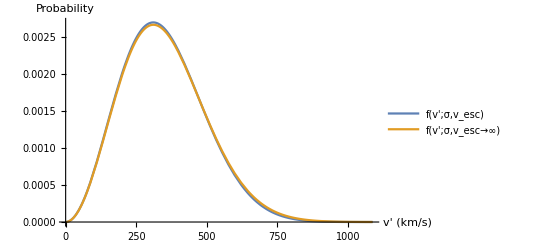

```mathematica
Plot[{feff[l,220 / Sqrt[2],544] / normalization,fnesc[l,220 / Sqrt[2]] },{l,0,2*544}, PlotLegends-> {"f(v';σ,v_esc)","f(v';σ,v_esc→∞)"}, AxesLabel->{"v' (km/s)","Probability"}]
```

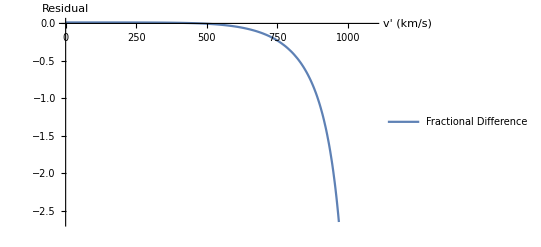

```mathematica
Plot[{ (feff[l,220 / Sqrt[2],544] / normalization - fnesc[l,220 / Sqrt[2] ] )/ (feff[l,220 / Sqrt[2],544] / normalization)},{l,0,2*544}, PlotLegends-> {"Fractional Difference"}, AxesLabel->{"v' (km/s)","Residual"}]
```

```mathematica
NIntegrate[F[vθ[u,l/2,544],220 / Sqrt[2]] * l^3 * Exp[-l^2 / (2*220^2)] , {u,0,1},{l,0,2*544}] / normalization
```

347.343

```mathematica
NIntegrate[fnesc[l,220 / Sqrt[2]] * l, {l,0,∞}]
```

351.069

```mathematica
fescapprox[l_,σ_]:=l^2 * Exp[-l^2 / (4*σ^2)]
normalizationapprox = NIntegrate[l^2 * Exp[-l^2 / (2*220^2)],{l,0,2*544}]
```

1.3345×10^7

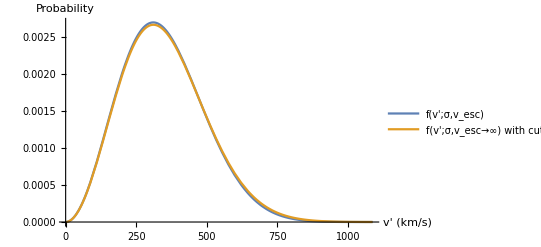

```mathematica
Plot[{feff[l,220 / Sqrt[2],544] / normalization,fescapprox[l,220 / Sqrt[2]] / normalizationapprox },{l,0,2*544}, PlotLegends-> {"f(v';σ,v_esc)","f(v';σ,v_esc→∞) with cutoff"}, AxesLabel->{"v' (km/s)","Probability"}]
```

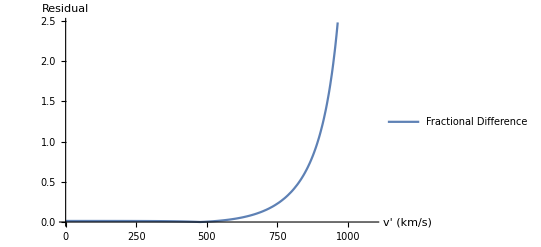

```mathematica
Plot[{ Abs[ ( feff[l,220 / Sqrt[2],544] / normalization - fescapprox[l,220 / Sqrt[2]] / normalizationapprox )  / (feff[l,220 / Sqrt[2],544] / normalization)] },{l,0,2*544}, PlotLegends-> {"Fractional Difference"}, AxesLabel->{"v' (km/s)","Residual"}]
```

```mathematica
NIntegrate[F[vθ[u,1,544],220 / Sqrt[2]],{u,0,1}]
```

68.9309

```mathematica
1 * Exp[-220/ (2 * 220^2)]
```

1/ⅇ^(1/440)

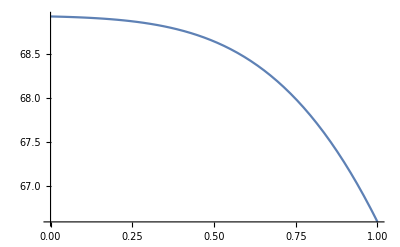

```mathematica
Plot[F[vθ[u,220,544],220 / Sqrt[2]], {u,0,1}]
```

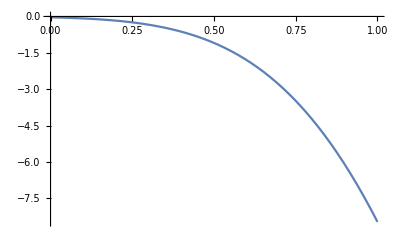

```mathematica
Plot[-2 ⅇ^(-vθ[u,220,544]^2/(220 / Sqrt[2])^2) vθ[u,220,544],{u,0,1}]
```

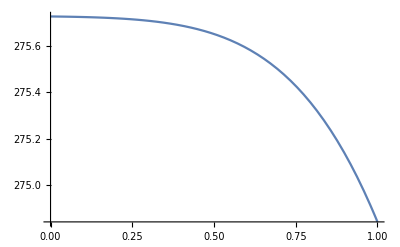

```mathematica
Plot[√π (220/Sqrt[2]) Erf[vθ[u,220,544]/(220/Sqrt[2])],{u,0,1}]
```